```mathematica
(* Notebook for investigating the scattering phase shift for massless Dirac particles in graphene *)
```

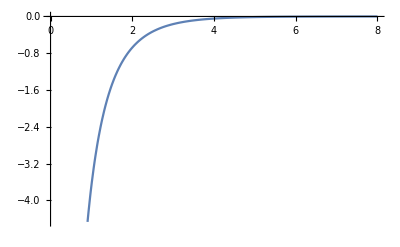

```mathematica
(* Define the potential, magnetic or scalar *)
ClearAll["Global`*"];
v=-5;
d=3;
a=2;
(*U[r_]:=Piecewise[{{v,d<r<(d+a)}},0];*)
U[r_]:=-10*Exp[-r]/r;

Plot[U[r],{r,0,8},Exclusions->None]
```

```mathematica
m=3;
k=0.1;
iterations=5;
p[r_]:=BesselJ[m,k r]Cos[δ[r]]-BesselY[m,k r]Sin[δ[r]];
JPRIME[r_]:=1/2(BesselJ[m-1,k*r]-BesselJ[m+1,k*r]);
YPRIME[r_]:=1/2(BesselY[m-1,k*a]-BesselY[m+1,k*r]);
q[r_]:=JPRIME[r]Cos[δ[r]]-YPRIME[r]Sin[δ[r]];
For[i=0,i<iterations,i++,δtemp=NDSolveValue[{δ'[r]==(r π)/2 p[r]((U'[r])/(k-U[r])(q[r]-m/r p[r])+((U[r])^2-2k U[r])p[r]),δ[0.1]==0},δ,{r,0.1,10}];
δ[r]=δtemp[r];]
Plot[δ[r]/π,{r,0.1,8},AxesLabel->{r,"δ(r)/π"}]
```

NDSolveValue::ndsz: At r == 0.108864, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1.09205} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.13432} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolveValue::ndsz: At r == 0.108863, step size is effectively zero; singularity or stiff system suspected.

NDSolveValue::mxst: Maximum number of 96445 steps reached at the point r == 0.109437.

NDSolveValue::mxst: Maximum number of 96445 steps reached at the point r == 0.10888.

-Graphics-

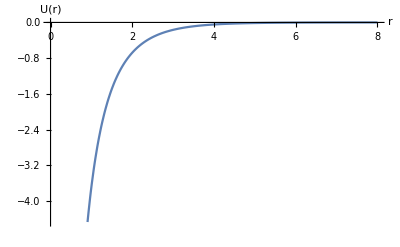

-Graphics-

```mathematica
Plot[U[r],{r,0,8},Exclusions->None,TicksStyle->Directive[Black, FontSize->48],AxesLabel->{r,"U(r)"},LabelStyle->Directive[Black,FontSize->48]]
Plot[(-δ[r])/π,{r,0.1,10},TicksStyle->Directive[Black, FontSize->48],AxesLabel->{r,"δ(r)/π"},LabelStyle->Directive[Black,FontSize->48],PlotRange->All]
```